```mathematica
Quit[];
```

```mathematica
<<FeynArts`
<<FormCalc`
```

FeynArts 3.11 (2 Sep 2019)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

FormCalc 9.9 (6 Oct 2019)

by Thomas Hahn

```mathematica
(* Create my topologies. *)
(* 0 loops, 2 incoming legs, 2 outgoing legs.*)
topologies=CreateTopologies[0,2 -> 2];
_Hel=0;
Print[topologies];
```

TopologyList[Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[4][5]],Propagator[Incoming][Vertex[1][2],Vertex[4][5]],Propagator[Outgoing][Vertex[1][3],Vertex[4][5]],Propagator[Outgoing][Vertex[1][4],Vertex[4][5]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][5]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][5]],Propagator[Outgoing][Vertex[1][4],Vertex[3][6]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]],Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][5]],Propagator[Incoming][Vertex[1][2],Vertex[3][6]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6]],Propagator[Outgoing][Vertex[1][4],Vertex[3][5]],Propagator[Internal][Vertex[3][5],Vertex[3][6]]]]

loading generic model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.gen

> $GenericMixing is OFF

generic model {DMsimp_s_spin1_vector} initialized

loading classes model file /Users/kpachal/Code/DMSP/FormCalc/FeynArts-3.11/Models/DMsimp_s_spin1_vector.mod

> 46 particles (incl. antiparticles) in 26 classes

> $CounterTerms are ON

> 147 vertices

> 48 counterterms of order 1

classes model {DMsimp_s_spin1_vector} initialized

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 1 Classes insertion

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

in total: 1 Classes insertion

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

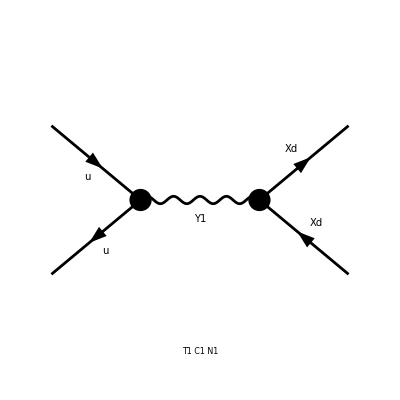

```mathematica
(* ExcludeParticles->{V[1],V[2],V[3],V[4],S[1],S[2]} *)
diagvec=InsertFields[topologies,{F[7,{1}],-F[7,{1}]}->{F[13],-F[13]},InsertionLevel->{Classes},
Model->"DMsimp_s_spin1_vector",
GenericModel->"DMsimp_s_spin1_vector"];
Paint[diagvec];
```

```mathematica
(* Calculate amplitude. *)
ClearProcess[];
amplist = CreateFeynAmp[diagvec];
amp=CalcFeynAmp[amplist,FermionChains->VA];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

in total: 1 Classes amplitude

preparing FORM code in /Users/kpachal/fc-amp-9.frm

running FORM...

ok

```mathematica
(* Done with FeynArts! Time to pass the amplitude to FormCalc. *)
(* Squared matrix elements; evaluate *)
squared = SquaredME[amp];
Print[squared];
```

{FF[F1] FFC[F1] Mat[F1,F1],{FF[F1]→-gc75 gc76 Den[S,MY1^2],FFC[F1]→-(gc75Superscript[*]) (gc76Superscript[*]) Den[S,(MY1Superscript[*])^2]}}

```mathematica
(* SquaredME returns a list of {squared, squaredRules}, where we should later apply "squaredRules" to "squared". *)
(* Because of the quarks, we do ColorME too. *)
cleanSquaredME = squared[[1]]//.squared[[2]]//.HelicityME[amp]//FullSimplify
```

> 1 helicity matrix elements

preparing FORM code in /Users/kpachal/fc-hel-10.frm

running FORM...

ok

1/2 gc75 gc76 (T^2+2 MXd^2 (MXd^2+S-T-U)+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* We want to sum over polarisations and make them go away: *)
TotalME = PolarizationSum[cleanSquaredME,GaugeTerms->False]//.Subexpr[]//.Abbr[]
```

preparing FORM code in /Users/kpachal/fc-pol-10.frm

running FORM...

ok

1/2 gc75 gc76 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gc75Superscript[*]) (gc76Superscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Convert vertices back to versions we know *)
TotalMEFinalVertices = TotalME//. M$FACouplings
```

1/2 gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]) Den[S,MY1^2] Den[S,(MY1Superscript[*])^2]

```mathematica
(* Sort out denominators. *)
TotalMEWithBWPropagator = TotalMEFinalVertices//.Den[a_,b_^2]Den[a_, Conjugate[b_]^2]:>1/((a - b^2)^2 + b^2 Gamma^2)
```

(gVu11 gVXd (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2) (gVu11Superscript[*]) (gVXdSuperscript[*]))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Tell Mathematica that my couplings, widths, and masses are positive real numbers *)
TotalMEClean = Refine[TotalMEWithBWPropagator, {Element[MY1,Reals],Element[gVXd,Reals],Element[gVu11,Reals],Element[Gamma,Reals], MY1>0, gVXd > 0, gVu11 > 0, Gamma >0}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+T^2+U^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Full clean matrix element obtained. Testing begins here. *)
```

```mathematica
(* Define variables we'll need for next integrals. *)
(* Based on materials here: http://scipp.ucsc.edu/~haber/ph217/Lips.pdf *)
(* a,b->1,2 *)
LambdaXd = (S - 4 MXd^2)S
Lambdaq = (S - 4 Mq^2) S
PrefixDSigDOhm = 1/(64 Pi^2 S) Sqrt[LambdaXd]/Sqrt[Lambdaq]
PrefixDSigDT = 1/(16 Pi Lambdaq)
```

S (-4 MXd^2+S)

S (-4 Mq^2+S)

(√(S (-4 MXd^2+S)))/(64 π^2 S √(S (-4 Mq^2+S)))

1/(16 π S (-4 Mq^2+S))

```mathematica
(* Variant 1: we are going to convert everything into s and cos theta, then integrate out cos theta. *)
(* Use the massive substitutions for Mandelstam variables. *)
TVal = Mq^2 + MXd^2 - S/2 + 1/(2S) Sqrt[Lambdaq] Sqrt[LambdaXd] Cos[Theta]
METheta = TotalMEClean//.{T -> TVal, U-> 2 Mq^2 + 2 MXd^2 - S - T}
```

Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S)

1/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)

```mathematica
(* We introduced Mq here so let's inform Mathematica about it too: *)
METhetaClean = Refine[METheta,{Element[Mq,Reals],Mq >0}]
```

1/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2)

```mathematica
(* From matrix element to cross section, using massive equation: *) 
dSigdOmega = PrefixDSigDOhm METhetaClean
Sigma1 = 2 Pi Integrate[dSigdOmega  Sin[Theta], {Theta, 0, Pi} ]
```

(gVu11^2 gVXd^2 √(S (-4 MXd^2+S)) (2 MXd^4-4 MXd^2 (MXd^2-S)+(Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2+(Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)) Cos[Theta])/(2 S))^2))/(128 π^2 S √(S (-4 Mq^2+S)) (Gamma^2 MY1^2+(-MY1^2+S)^2))

(gVu11^2 gVXd^2 √(S (-4 MXd^2+S)) (3 Mq^4+2 Mq^2 (5 MXd^2-2 S)+S (2 MXd^2+S)))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) S √(S (-4 Mq^2+S)))

```mathematica
(* Variant 2: we are going to convert everything into s and t, then integrate out t. *)
(* Keep the massive substitutions for Mandelstam variables. *)
MEMandelstamT = TotalMEClean//.{U-> 2 Mq^2 + 2 MXd^2 - S - T}
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(2 Mq^2+2 MXd^2-S-T)^2+T^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* Again we introduced Mq here, so let's inform Mathematica about this one too: *)
MEMandelstamClean = Refine[MEMandelstamT,{Element[Mq,Reals],Mq >0}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(2 Mq^2+2 MXd^2-S-T)^2+T^2))/(2 (Gamma^2 MY1^2+(-MY1^2+S)^2))

```mathematica
(* From matrix element to cross section: *)
dSigdt = PrefixDSigDT MEMandelstamClean
tMin = TVal//.Theta->Pi
tMax = TVal//.Theta->0
(* We were integrating from -S to 0 but this was an approximation. *)
Sigma2 = Integrate[dSigdt, {T, tMin, tMax}]
```

(gVu11^2 gVXd^2 (2 MXd^4-4 MXd^2 (MXd^2-S)+(2 Mq^2+2 MXd^2-S-T)^2+T^2))/(32 π S (-4 Mq^2+S) (Gamma^2 MY1^2+(-MY1^2+S)^2))

Mq^2+MXd^2-S/2-(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)))/(2 S)

Mq^2+MXd^2-S/2+(√(S (-4 Mq^2+S)) √(S (-4 MXd^2+S)))/(2 S)

(gVu11^2 gVXd^2 √(S (-4 MXd^2+S)) (3 Mq^4+2 Mq^2 (5 MXd^2-2 S)+S (2 MXd^2+S)))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) S √(S (-4 Mq^2+S)))

```mathematica
(* Are these the same? *)
(* Let's find out. *)
Sigma1==Sigma2
```

True

```mathematica
(* Great! Then it doesn't matter which one we use. *)
(* Let's simplify here by setting Mq to zero. *)
(* Also let it know S is positive. *)
SigmaMassless = Refine[Sigma1//.{Mq->0},S>0]
```

(gVu11^2 gVXd^2 √(-4 MXd^2+S) (2 MXd^2+S))/(48 π (Gamma^2 MY1^2+(MY1^2-S)^2) √S)

```mathematica
(* This has pretty much the expected breit-wigner shape still *)
(* The limit is zero at infinity and it is zero at S = 4 MXd^2. *)
(* It falls proportionally to 1/S. *)
(* Yet the integral calculation is a mess. What can I do about it? *)
(* Checking Gradshteyn & Ryzhik*)
```

```mathematica
(* Trial: set masses etc and then do the integral. *)
(* Use the ones I had in my WA test. *)
ExampleSigma = SigmaMassless//.{MXd->1, MY1->10,Gamma->0.1, gVu11->1, gVXd->1}
thisInt = Integrate[ExampleSigma,S]
```

(√(-4+S) (2+S))/(48 π (1.+(100-S)^2) √S)

1/(√(-1. (-4.+S)^2))0.00663146 √(-4.+S) √((-4+S)/S) (2. √S ArcSin[√(1.-0.25 S)]-(1.+102. ⅈ) √(4.-1. S) Hypergeometric2F1[0.5,1.,1.5,(1.04166+0.000433981 ⅈ)-(4.16665+0.00173592 ⅈ)/S]-(1.-102. ⅈ) √(4.-1. S) Hypergeometric2F1[0.5,1.,1.5,(1.04166-0.000433981 ⅈ)-(4.16665-0.00173592 ⅈ)/S])

```mathematica
Limit[thisInt,S->Infinity]
```

∞

```mathematica
(* Do the integral. *)
TotalSigma = Integrate[SigmaMassless, S]
```

```mathematica
1/(48 π)gVu11^2 gVXd^2 ((2 MXd √(4-S/MXd^2) ArcSin[(√S)/(2 MXd)])/(√(-4 MXd^2+S))+(√(4 MXd^2+(√(-Gamma^2)-MY1) MY1) (2 √(-Gamma^2) MXd^2+MY1 (Gamma^2+√(-Gamma^2) MY1)) ArcTan[(√(4 MXd^2+(√(-Gamma^2)-MY1) MY1) √S)/(√(MY1 (-√(-Gamma^2)+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(MY1 (-√(-Gamma^2)+MY1)))+(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) (-2 √(-Gamma^2) MXd^2+MY1 (Gamma^2-√(-Gamma^2) MY1)) ArcTan[(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) √S)/(√(-MY1 (√(-Gamma^2)+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(-MY1 (√(-Gamma^2)+MY1))))
```

```mathematica
(* No log divergence this time. But looks like quite possibly loads of other divergences. *)
(* SigmaTotApproximate = FullSimplify[Refine[TotalSigma//.{Log[a_]->0}]] *)
(* Do some clean up and see if we can get this in a more reasonable form. *)
SigmaTot2 = TotalSigma//.{Sqrt[-Gamma^2]-> ⅈ Gamma}
```

1/(48 π)gVu11^2 gVXd^2 ((2 MXd √(4-S/MXd^2) ArcSin[(√S)/(2 MXd)])/(√(-4 MXd^2+S))+(√(4 MXd^2+(ⅈ Gamma-MY1) MY1) (2 ⅈ Gamma MXd^2+MY1 (Gamma^2+ⅈ Gamma MY1)) ArcTan[(√(4 MXd^2+(ⅈ Gamma-MY1) MY1) √S)/(√(MY1 (-ⅈ Gamma+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(MY1 (-ⅈ Gamma+MY1)))+(√(-4 MXd^2+MY1 (ⅈ Gamma+MY1)) (-2 ⅈ Gamma MXd^2+MY1 (Gamma^2-ⅈ Gamma MY1)) ArcTan[(√(-4 MXd^2+MY1 (ⅈ Gamma+MY1)) √S)/(√(-MY1 (ⅈ Gamma+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(-MY1 (ⅈ Gamma+MY1))))

```mathematica
(* Can I do anything with this? Is the low end even real? *)
SigmaLow = Limit[SigmaTot2,S->4MXd^2]
```

Indeterminate

```mathematica
(* Let's try forcing some manual cleanup. *) 
SigmaTot2 = Simplify[SigmaTotApproximate Sqrt[MY1(-Sqrt[-Gamma^2] + MY1)]]
```

1/(48 π)gVu11^2 gVXd^2 √(MY1 (-√(-Gamma^2)+MY1)) ((2 MXd √(4-S/MXd^2) ArcCsc[(2 MXd)/(√S)])/(√(-4 MXd^2+S))+(√(4 MXd^2+(√(-Gamma^2)-MY1) MY1) (Gamma^2 MY1+√(-Gamma^2) (2 MXd^2+MY1^2)) ArcTan[(√(4 MXd^2+(√(-Gamma^2)-MY1) MY1) √S)/(√(MY1 (-√(-Gamma^2)+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(MY1 (-√(-Gamma^2)+MY1)))+(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) (Gamma^2 MY1-√(-Gamma^2) (2 MXd^2+MY1^2)) ArcTan[(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) √S)/(√(-MY1 (√(-Gamma^2)+MY1)) √(-4 MXd^2+S))])/(Gamma^2 MY1 √(-MY1 (√(-Gamma^2)+MY1))))

```mathematica
(* Test: can I get limit from this now? *)
TestIntApproxUpper = Limit[SigmaTotApproximate,S->Infinity]
```

∞ Sign[gVu11]^2 Sign[gVXd]^2

```mathematica
(* Equivalent of definite integral is SigmaTotApproximate|infinity - SigmaTotApproximate|2MXd *)
(* Limit not working so I am doing it myself. *)
DefiniteIntApproxUpper = SigmaTotAppx2//.{ArcTan[(MY1^2 -S)/(Gamma MY1)]->-Pi/2,ArcTan[(-MY1^2+S)/(Gamma MY1)]->Pi/2}
DefiniteIntApproxLower = SigmaTotApprx2//.{S->4MXd^2}
```

(gVu11^2 gVXd^2 √(-4 Mq^2+S) √(S (-4 MXd^2+S)) ((2 Mq^2 (3 Mq^2+10 MXd^2) ArcSinh[(√(-4 Mq^2+S))/(2 √(Mq^2-MXd^2))])/(√(Mq^2-MXd^2) √((-4 MXd^2+S)/(Mq^2-MXd^2)))-((3 Mq^4 (√(-Gamma^2)+MY1)+MY1 (Gamma^2+MY1^2) (2 MXd^2+MY1 (-√(-Gamma^2)+MY1))+2 Mq^2 (5 MXd^2 (√(-Gamma^2)+MY1)-2 MY1 (Gamma^2+MY1^2))) ArcSinh[(√(-4 Mq^2+S))/(2 √(Mq^2-MXd^2))])/(√(-Gamma^2) √(Mq^2-MXd^2) √((-4 MXd^2+S)/(Mq^2-MXd^2)))+((-3 Mq^4 (√(-Gamma^2)-MY1)+MY1 (Gamma^2+MY1^2) (2 MXd^2+MY1 (√(-Gamma^2)+MY1))-2 Mq^2 (5 MXd^2 (√(-Gamma^2)-MY1)+2 MY1 (Gamma^2+MY1^2))) ArcSinh[(√(-4 Mq^2+S))/(2 √(Mq^2-MXd^2))])/(√(-Gamma^2) √(Mq^2-MXd^2) √((-4 MXd^2+S)/(Mq^2-MXd^2)))-(√(-4 MXd^2+MY1 (-√(-Gamma^2)+MY1)) (3 Mq^4 (√(-Gamma^2)+MY1)+MY1 (Gamma^2+MY1^2) (2 MXd^2+MY1 (-√(-Gamma^2)+MY1))+2 Mq^2 (5 MXd^2 (√(-Gamma^2)+MY1)-2 MY1 (Gamma^2+MY1^2))) ArcTan[(√(-4 MXd^2+MY1 (-√(-Gamma^2)+MY1)) √(-4 Mq^2+S))/(√(4 Mq^2+(√(-Gamma^2)-MY1) MY1) √(-4 MXd^2+S))])/(√(-Gamma^2) √(4 Mq^2+(√(-Gamma^2)-MY1) MY1) √(-4 MXd^2+S))+(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) (-3 Mq^4 (√(-Gamma^2)-MY1)+MY1 (Gamma^2+MY1^2) (2 MXd^2+MY1 (√(-Gamma^2)+MY1))-2 Mq^2 (5 MXd^2 (√(-Gamma^2)-MY1)+2 MY1 (Gamma^2+MY1^2))) ArcTan[(√(-4 MXd^2+MY1 (√(-Gamma^2)+MY1)) √(-4 Mq^2+S))/(√(4 Mq^2-MY1 (√(-Gamma^2)+MY1)) √(-4 MXd^2+S))])/(√(-Gamma^2) √(4 Mq^2-MY1 (√(-Gamma^2)+MY1)) √(-4 MXd^2+S))-(2 Mq MXd (3 Mq^2+10 MXd^2) ArcTanh[(MXd √(-4 Mq^2+S))/(Mq √(-4 MXd^2+S))])/(√(-4 MXd^2+S))))/(48 MY1^2 (Gamma^2+MY1^2) π √(S (-4 Mq^2+S)))

Power::infy: Infinite expression \!\(\*FractionBox["1", SqrtBox["0"]]\) encountered.

General::stop: Further output of \!\(\*StyleBox[RowBox[{"Power", "::", "infy"}], "MessageName"]\) will be suppressed during this calculation.

Indeterminate

```mathematica
(* Finally, expression I want is difference of those. *)
FinalExpression = Simplify[DefiniteIntApproxUpper - DefiniteIntApproxLower]
```

```mathematica
(* One way to clean this up: arctan(-x) = - arctan(x) *)
CleanFinal = Simplify[FinalExpression//.ArcTan[(-4MXd^2 + MY1^2)/(Gamma MY1)]->-ArcTan[(4MXd^2 - MY1^2)/(Gamma MY1)]]
```

```mathematica
(* In case I need more simplification, drop Mq: *)
CleanFinalSimple = CleanFinal//.Mq->0
```

```mathematica
(* OK, that looks non-terrible. Gamma in the demoninator is a non-issue since this is total width, not Gamma_DM *)
(* Let's do a few checks: what does it simplify down to in on-shell and off-shell cases? *)
(* Very on-shell: MY1 >> MXd. Let initial and final state masses both go to zero. *)
(* MY1 >> Gamma also, so ArcTan[MY1/Gamma] -> Pi/2 *)
OnShellLimit = CleanFinal//.{MXd -> 0, Mq->0, ArcTan[MY1/Gamma]-> Pi/2}
```

```mathematica
(* Very off-shell: MY1 << 2 MXd. *)
(* This will make Mathematica barf without some help on the arctan. *)
OffShellLimit = CleanFinal//.{ArcTan[(4 MXd^2 - MY1^2)/(Gamma MY1)]-> -Pi/2, MY1->0}
```